```mathematica
x^2+2 x+7==0
Solve[x^2+2 x+7==0,x]
```

7+2 x+x^2==0

{{x→-1-ⅈ √6},{x→-1+ⅈ √6}}

```mathematica
sol=Solve[x^2+2 x-7==0,x]
```

```mathematica
{{x->-1-2 √2},{x->-1+2 √2}}
```

```mathematica
sol[[1]]
```

{x→-1-2 √2}

```mathematica
Replace[x,sol[[1]]]
```

-1-2 √2

```mathematica
x+1/.sol[[1]]
```

-2 √2

```mathematica
Replace[x+1,x+1->5]
```

5

```mathematica
x^2/.sol[[1]]
```

(-1-2 √2)^2

```mathematica
Solve[x^5+12 x^3-5 x+8==0,x]
```

{{x→-1},{x→Root-0.0252-3.52 ⅈRoot[8-13 #1+13 #1^2-#1^3+#1^4&,1]-0.025158245527528995},{x→Root-0.0252+3.52 ⅈRoot[8-13 #1+13 #1^2-#1^3+#1^4&,2]-0.025158245527528995},{x→Root0.525-0.607 ⅈRoot[8-13 #1+13 #1^2-#1^3+#1^4&,3]0.525158245527529},{x→Root0.525+0.607 ⅈRoot[8-13 #1+13 #1^2-#1^3+#1^4&,4]0.525158245527529}}

```mathematica
NSolve[x^5+12 x^3-5 x+8==0,x]
```

{{x→-1.},{x→-0.0251582-3.52242 ⅈ},{x→-0.0251582+3.52242 ⅈ},{x→0.525158-0.607411 ⅈ},{x→0.525158+0.607411 ⅈ}}

```mathematica
Solve[a x+b==0,x]
```

{{x→-b/a}}

```mathematica
Reduce[a x+b==0,x]
```

(b==0&&a==0)||(a≠0&&x==-b/a)

```mathematica
Solve[3 x-2≤0,x]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
Reduce[3 x-2≤0,x]
```

x≤2/3

```mathematica
Solve[Cos[x]==x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Cos[x]==x,x]

```mathematica
NSolve[Cos[x]==x,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Cos[x]==x,x]

```mathematica
Reduce[Cos[x]==x,x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[x]==x,x]

```mathematica
FindRoot[Cos[x]==x,{x,-1000}]
```

{x→0.739085}

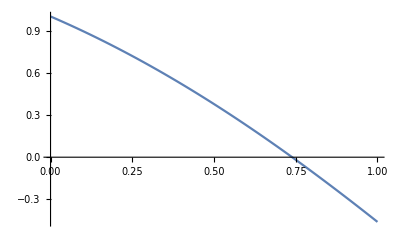

```mathematica
Plot[Cos[x]-x,{x,0,1}]
```

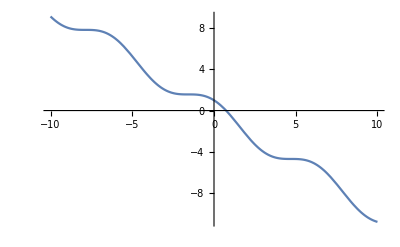

```mathematica
Plot[Cos[x]-x,{x,-10,10}]
```

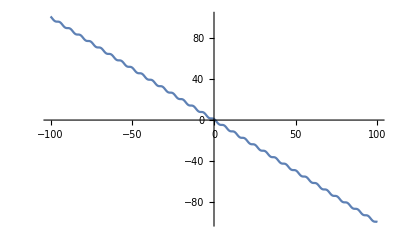

```mathematica
Plot[Cos[x]-x,{x,-100,100}]
```

```mathematica
FindRoot[x^(1/3)==0,{x,0.1}]
```

{x→4.44589×10^-16-5.55387×10^-29 ⅈ}

```mathematica
FindRoot[x^(1/3)==0,{x,0}]
```

{x→0.}

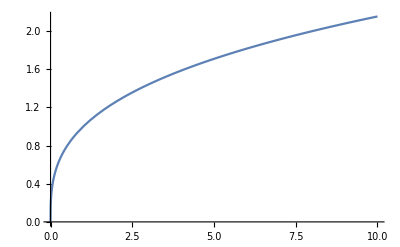

```mathematica
Plot[x^(1/3),{x,0,10}]
```

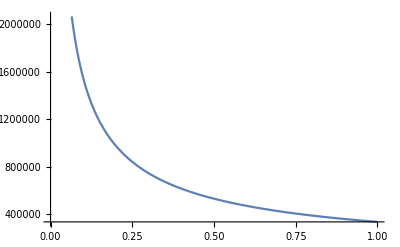

```mathematica
Plot[D[x^(1/3),x]/.x->y,{y,0,0.000000001}]
```

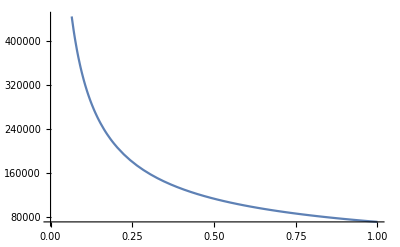

```mathematica
Plot[D[x^(1/3),x]/.x->y,{y,0,0.00000001}]
```

```mathematica
FindRoot[2+x^3-x-Sin[x]==0,{x,0}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.758482}

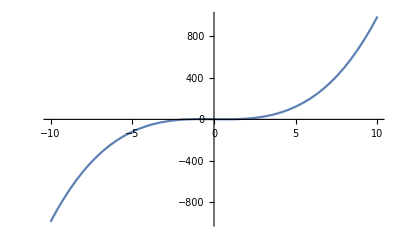

```mathematica
Plot[2+x^3-x-Sin[x],{x,-10,10}]
```

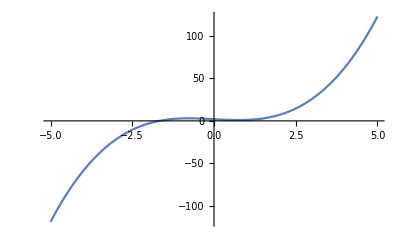

```mathematica
Plot[2+x^3-x-Sin[x],{x,-5,5}]
```

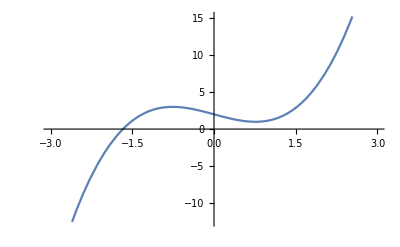

```mathematica
Plot[2+x^3-x-Sin[x],{x,-3,3}]
```

```mathematica
s=FindRoot[2+x^3-x-Sin[x]==0,{x,-2}]
```

{x→-1.67102}

```mathematica
2+x^3-x-Sin[x]/.s
```

-4.44089×10^-16

```mathematica
(*Task1a*)
```

```mathematica
M={{2,1},{3,-1}};
b={0,2};
```

```mathematica
Det[M]
```

-5

```mathematica
Solve[{2 x+y==0,3 x-y==2},{x,y}]
```

{{x→2/5,y→-4/5}}

```mathematica
Inverse[M].b
```

{2/5,-4/5}

```mathematica
point=LinearSolve[M,b]
```

{2/5,-4/5}

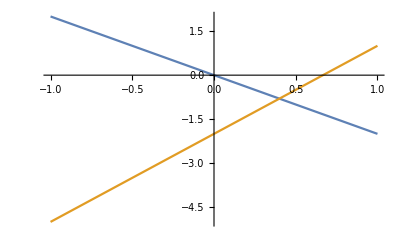

```mathematica
Plot[{-2 x,3 x-2},{x,-1,1}]
```

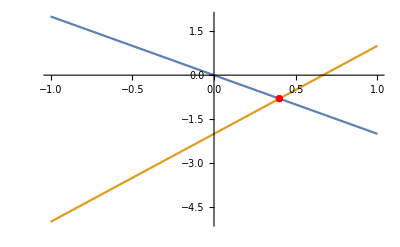

```mathematica
Show[Plot[{-2 x,3 x-2},{x,-1,1}],ListPlot[{point},PlotStyle->Red]]
```

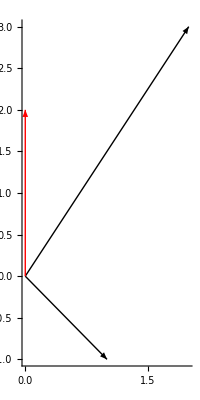

```mathematica
Graphics[{Arrow[{{0,0},{2,3}}],Arrow[{{0,0},{1,-1}}],Red,Thick,Arrow[{{0,0},{0,2}}]},Axes->True]
```

```mathematica
(*Task1b*)
M={{2,1},{2,1}};
b={0,2};
```

```mathematica
LinearSolve[M,b]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{2,1},{2,1}},{0,2}]

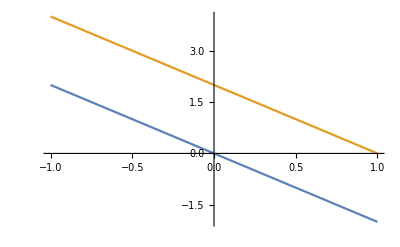

```mathematica
Plot[{-2 x,-2 x+2},{x,-1,1}]
```

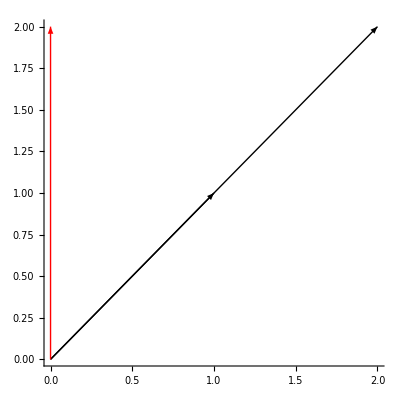

```mathematica
Graphics[{Arrow[{{0,0},{2,2}}],Arrow[{{0,0},{1,1}}],Red,Thick,Arrow[{{0,0},{0,2}}]},Axes->True]
```

```mathematica
(*Task1c*)
M={{2,1},{2,1}};
b={3,3};
```

```mathematica
point=LinearSolve[M,b]
```

{3/2,0}

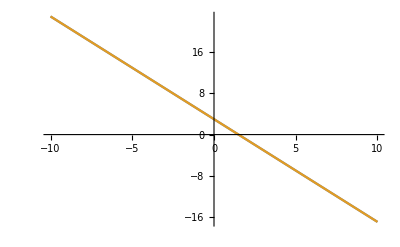

```mathematica
Plot[{3-2 x,3-2 x},{x,-10,10}]
```

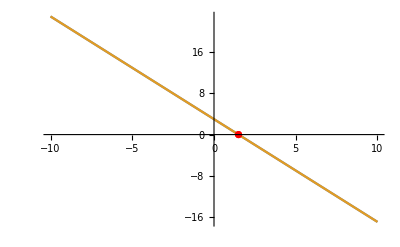

```mathematica
Show[Plot[{3-2 x,3-2 x},{x,-10,10}],ListPlot[{point},PlotStyle->Red]]
```

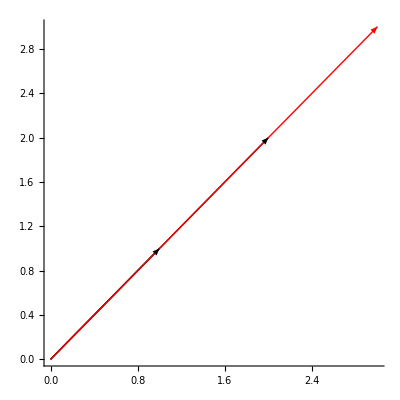

```mathematica
Graphics[{Arrow[{{0,0},{2,2}}],Arrow[{{0,0},{1,1}}],Red,Thick,Arrow[{{0,0},{3,3}}]},Axes->True]
```

```mathematica
(*Task1d*)
M={{3,2,-1},{2,-2,4},{-1,8,-1}};
b={1,-2,0};
```

```mathematica
point=LinearSolve[M,b]
```

{1/6,-1/18,-11/18}

```mathematica
Det[M]
```

-108

```mathematica
MatrixRank[M]
```

3

```mathematica
ContourPlot3D[{3 x+2 y-z==1,2 x-2 y+4 z==-2,-x+8 y-z==0},{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[{3 x+2 y-z==1,2 x-2 y+4 z==-2,-x+8 y-z==0},{x,-10,10},{y,-10,10},{z,-10,10}],ListPointPlot3D[{point},PlotStyle->{Red,PointSize[0.05]}]]
```

-Graphics3D-

```mathematica
NullSpace[M]
```

{}

```mathematica
(*Task2a*)
Solve[x^4==E^x,x,Reals]
```

{{x→-4 ProductLog[-1/4]},{x→-4 ProductLog[1/4]},{x→-4 ProductLog[-1,-1/4]}}

```mathematica
NSolve[x^4==E^x,x,Reals]
```

{{x→-0.815553},{x→1.42961},{x→8.61317}}

```mathematica
Reduce[x^4==E^x,x,Reals]
```

x==-4 ProductLog[-1/4]||x==-4 ProductLog[1/4]||x==-4 ProductLog[-1,-1/4]

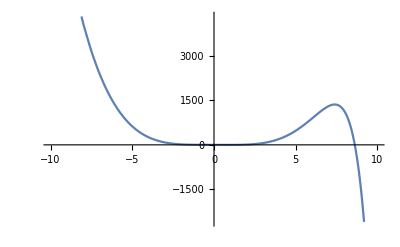

```mathematica
Plot[x^4-E^x,{x,-10,10}]
```

```mathematica
FindRoot[x^4==E^x,{x,{0,1,8}}]
```

{x→{-0.815553,1.42961,8.61317}}

```mathematica
(*Task2b*)
Solve[10^(-0.1* x^2)==√(2 π+x)+Sin[2 x],x]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[10^(-0.1 x^2)==√(2 π+x)+Sin[2 x],x]

```mathematica
NSolve[10^(-0.1 *x^2)==√(2 π+x)+Sin[2 x],x]
```

NSolve[10^(-0.1 x^2)==√(2 π+x)+Sin[2 x],x]

```mathematica
Reduce[10^(-0.1 x^2)==√(2 π+x)+Sin[2 x],x]
```

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[10^(-0.1 x^2)==√(2 π+x)+Sin[2 x],x]

```mathematica
Plot[10 E^(-0,1 x^2)-√(2 π+x)-Sin[2 x],{x,-7,4}]
```

```mathematica
FindRoot[10^(-0.1* x^2)==√(2* π+x)+Sin[2 *x],{x,-4},EvaluationMonitor->Print[x]]
```

x

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→-3.99833}